```mathematica
IsotopeData[{8,22},"BindingEnergy"]
```

7.364821

```mathematica
IsotopeData[{6,12},"AtomicMass"]
```

12.

```mathematica
IsotopeData[{9,22},"ExcitedStateEnergies"]
```

{71.6,310.,709.,1420.,1627.6,2015.,2572.2,2990.,3170.,3380.,3590.,3980.,4200.,4365.,4630.,4780.,4885.,5235.,5590.,5750.,6595.}

```mathematica
ListPlot[Table[IsotopeData[{Z,10},"ExcitedStateEnergies"],{Z,6,7}]]
```

ListPlot::lpn: {{3353.6, 5220., 5380., 6580.}, {}} is not a list of numbers or pairs of numbers.

ListPlot[{{3353.6,5220.,5380.,6580.},{}}]

```mathematica
ListPlot3D[Table[IsotopeData[{Z,Z+n},"BindingEnergy"],{Z,6,30},{n,4,40}],Mesh->None,InterpolationOrder->0,ColorFunction->"Rainbow"]
```

IsotopeData::notent: "{6, 23}" is not a known entity, class, or tag for IsotopeData. Use IsotopeData[] for a list of entities.

IsotopeData::notent: "{6, 24}" is not a known entity, class, or tag for IsotopeData. Use IsotopeData[] for a list of entities.

IsotopeData::notent: "{6, 25}" is not a known entity, class, or tag for IsotopeData. Use IsotopeData[] for a list of entities.

General::stop: Further output of IsotopeData :: notent will be suppressed during this calculation.

-Graphics3D-

IsotopeData::notent: "{6, 23}" is not a known entity, class, or tag for IsotopeData. Use IsotopeData[] for a list of entities.

IsotopeData::notent: "{6, 24}" is not a known entity, class, or tag for IsotopeData. Use IsotopeData[] for a list of entities.

IsotopeData::notent: "{6, 25}" is not a known entity, class, or tag for IsotopeData. Use IsotopeData[] for a list of entities.

General::stop: Further output of IsotopeData :: notent will be suppressed during this calculation.

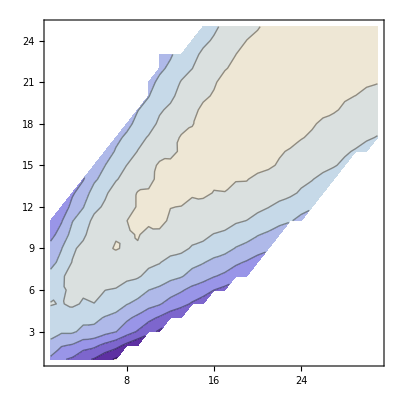

```mathematica
ListContourPlot[Table[IsotopeData[{Z,Z+n},"BindingEnergy"],{Z,6,30},{n,10,40}]]
```